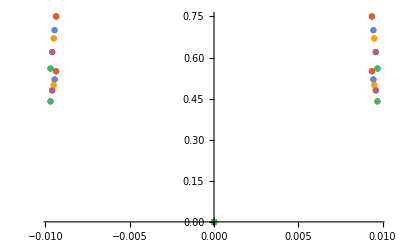

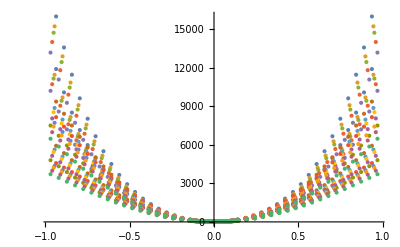

```mathematica
(*IMPORTANT - doubel check the eigenspectrum against standard harmonic DoS *)
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
(*Data in*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
filesC={"C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZr={"Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};
filesCh={"1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805","1.harm.C_4685_760_110","1.harm.C_4730_1900_110","1.harm.C_4759_2500_110","1.harm.C_4801_3200_110","1.harm.C_4850_3805_110","1.harm.C_4685_760_111","1.harm.C_4730_1900_111","1.harm.C_4759_2500_111","1.harm.C_4801_3200_111","1.harm.C_4850_3805_111"};
filesZrh={"1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805","1.harm.Zr_4685_760_110","1.harm.Zr_4730_1900_110","1.harm.Zr_4759_2500_110","1.harm.Zr_4801_3200_110","1.harm.Zr_4850_3805_110","1.harm.Zr_4685_760_111","1.harm.Zr_4730_1900_111","1.harm.Zr_4759_2500_111","1.harm.Zr_4801_3200_111","1.harm.Zr_4850_3805_111"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,15}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,15}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,15}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,15}];
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,15}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,15}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]

V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,15}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,15}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]
```

```mathematica
(*Solve carbon harmonic and anharmonic, first vol, 001 direction*)
ℒallch=Table[-(1/(2m[[1]]))*u''[x]+V[1,2,x][[1]]*u[x],{i,1,1}];
ℒallca=Table[-(1/(2m[[1]]))*u''[x]+V[1,6,x][[1]]*u[x],{i,1,1}];
(*Solve carbon harmonic and anharmonic, first vol, 001 direction*)
ℒallzh=Table[-(1/(2m[[2]]))*u''[x]+V[2,2,x][[1]]*u[x],{i,1,1}];
ℒallza=Table[-(1/(2m[[2]]))*u''[x]+V[2,6,x][[1]]*u[x],{i,1,1}];
```

```mathematica
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=300;
(*Define bounds for plotting and solving eigenproblem*)
B=1.2;H=2000;
(*Solveroptions*)
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}};
```

```mathematica
(*Solve eigensystems*)
eigensysch=Table[NDEigensystem[ℒallch[[j]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,1}];
eigensysca=Table[NDEigensystem[ℒallca[[j]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,1}];
eigensyszh=Table[NDEigensystem[ℒallzh[[j]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,1}];
eigensysza=Table[NDEigensystem[ℒallza[[j]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,1}];
```

InterpolatingFunction::dmval: Input value {-1.49994} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

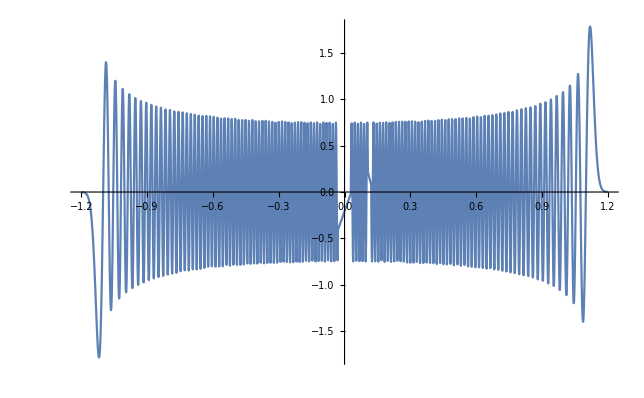

```mathematica
Plot[eigensysch[[1]][[2]][[250]],{x,-1.5,1.5},PlotRange->All]
```

```mathematica
DumpSave["dump.eigensysch.mx",eigensysch]
DumpSave["dump.eigensysca.mx",eigensysca]
DumpSave["dump.eigensyszh.mx",eigensyszh]
DumpSave["dump.eigensysza.mx",eigensysza]
```

```mathematica
Get["dump.eigensysch.mx"]
Get["dump.eigensysca.mx"]
Get["dump.eigensyszh.mx"]
Get["dump.eigensysza.mx"]
```

```mathematica
maxV=150;
charval=eigensysch[[1]][[1]][[1;;maxV]];
charvec=eigensysch[[1]][[2]][[1;;maxV]];
canhval=eigensysca[[1]][[1]][[1;;maxV]];
canhvec=eigensysca[[1]][[2]][[1;;maxV]];
zharval=eigensyszh[[1]][[1]][[1;;maxV]];
zharvec=eigensyszh[[1]][[2]][[1;;maxV]];
zanhval=eigensysza[[1]][[1]][[1;;maxV]];
zanhvec=eigensysza[[1]][[2]][[1;;maxV]];
```

```mathematica
(*Occupation functions - partition and Bose-Einstein*)
Z[eval_,T_]:=N[Sum[Exp[-eval[[i]]/(K2meV*T)],{i,1,Length[eval]}],20]
n[eval_,T_]:=1/(Exp[(eval)/(kB*T)]-1)

(*Density matrices*)

denMatKernal[eval_,evec_,T_]:=Sum[Exp[-eval[[i]]/(K2meV*T)]*evec[[i]]*evec[[i]],{i,1,Length[eval]}]
denMatKernalExpect[kernel_,eval_,T_]:=(1/Z[eval,T])*NIntegrate[kernel,{x,-0.7,0.7}]

densMatSpectrum[O_,eval_,evec_,T_]:=(1/Z[eval,T])*O*Table[Exp[-eval[[i]]/(K2meV*T)]*evec[[i]]*evec[[i]],{i,1,Length[eval]}]

densMatOperator[O_,eval_,evec_,T_]:=(1/Z[eval,T])*O*Sum[Exp[-eval[[i]]/(K2meV*T)]*evec[[i]]*evec[[i]],{i,1,Length[eval]}]

densMatExpect[O_,eval_,evec_,T_]:=(1/Z[eval,T])*NIntegrate[O*Sum[Exp[-eval[[i]]/(K2meV*T)]*evec[[i]]*evec[[i]],{i,1,Length[eval]}],{x,-0.7,0.7}]
```

```mathematica
Evaluate@V[1,6,x][[1]]
Evaluate@V[2,6,x][[1]]
charval[[1]]
zharval[[1]]
canhval[[1]]
zanhval[[1]]
```

6256.47 x^2+6879.88 x^4+1626.02 x^6

8508.33 x^2+8953.3 x^4+2418.13 x^6

16.1489

6.84261

16.1728

6.83325

## Position representation reduced density matrix expectation of harmonic and anharmonic potentials; The expectation is plotted as a function of positions along (001) for Zr and C at 500K intervals from up to 5000K

```mathematica
(*Options*)
B=1;
plotOpts={AxesLabel->{"x (Å)","⟨V(x)⟩ (meV/Å/atom)"}};
```

Carbon V(x) vs distance:

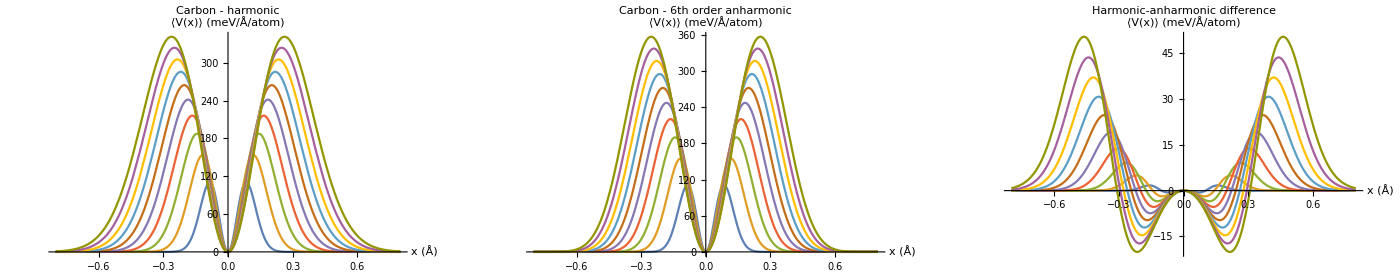

Zr V(x) vs distance:

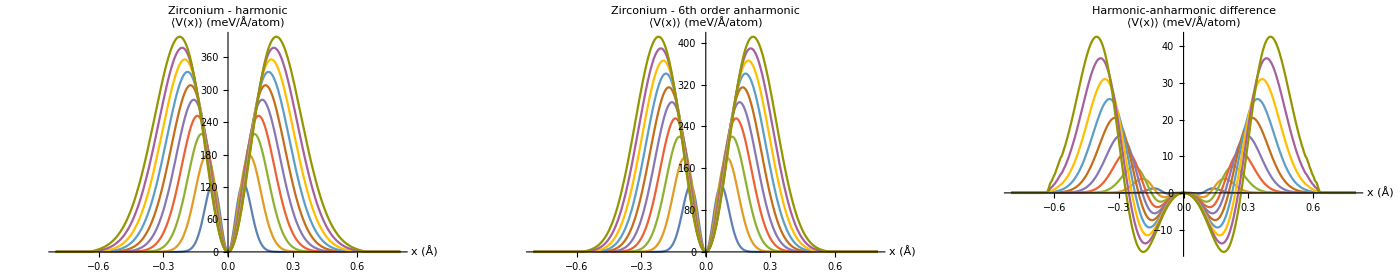

```mathematica
(*carbon and zr harmonic and 6th order anharmonic Potential V[X] expectation and difference*)
"Carbon V(x) vs distance:"
GraphicsGrid[
{{Plot[Evaluate@Table[densMatOperator[Evaluate@V[1,2,x][[1]],charval,charvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Carbon - harmonic",Evaluate@plotOpts],Plot[Evaluate@Table[densMatOperator[Evaluate@V[1,6,x][[1]],canhval,canhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Carbon - 6th order anharmonic",Evaluate@plotOpts],Plot[Evaluate@Table[densMatOperator[Evaluate@V[1,2,x][[1]],charval,charvec,500*i]-densMatOperator[Evaluate@V[1,6,x][[1]],canhval,canhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Harmonic-anharmonic difference",Evaluate@plotOpts]}},ImageSize->1400]
"Zr V(x) vs distance:"
GraphicsGrid[
{{Plot[Evaluate@Table[densMatOperator[Evaluate@V[2,2,x][[1]],zharval,zharvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Zirconium - harmonic",Evaluate@plotOpts],Plot[Evaluate@Table[densMatOperator[Evaluate@V[2,6,x][[1]],zanhval,zanhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Zirconium - 6th order anharmonic",Evaluate@plotOpts],Plot[Evaluate@Table[densMatOperator[Evaluate@V[2,2,x][[1]],zharval,zharvec,500*i]-densMatOperator[Evaluate@V[2,6,x][[1]],zanhval,zanhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Harmonic-anharmonic difference",Evaluate@plotOpts]}},ImageSize->1400]
```

150 eigenfunctions Less only

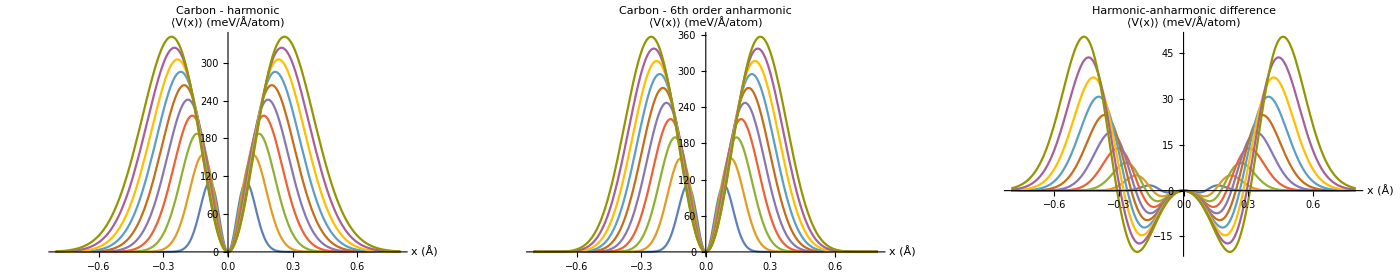

Zr V(x) vs distance:

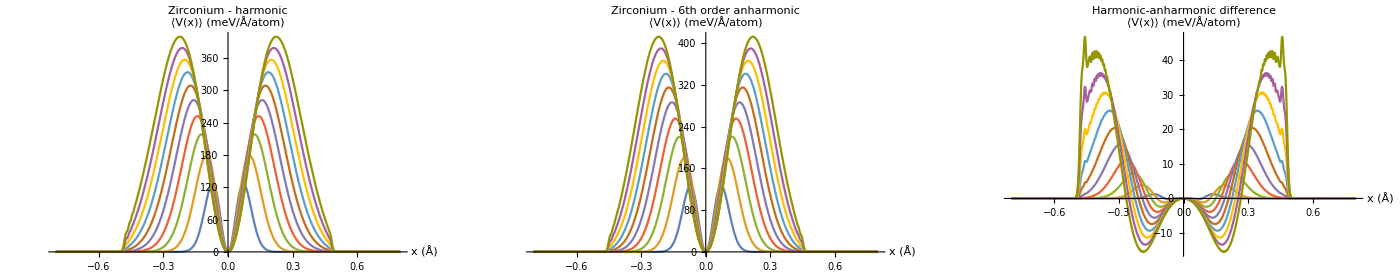

```mathematica
Less eigenfunctions only 150
GraphicsGrid[
{{Plot[Evaluate@Table[densMatOperator[Evaluate@V[1,2,x][[1]],charval,charvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Carbon - harmonic",Evaluate@plotOpts],Plot[Evaluate@Table[densMatOperator[Evaluate@V[1,6,x][[1]],canhval,canhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Carbon - 6th order anharmonic",Evaluate@plotOpts],Plot[Evaluate@Table[densMatOperator[Evaluate@V[1,2,x][[1]],charval,charvec,500*i]-densMatOperator[Evaluate@V[1,6,x][[1]],canhval,canhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Harmonic-anharmonic difference",Evaluate@plotOpts]}},ImageSize->1400]
"Zr V(x) vs distance:"
GraphicsGrid[
{{Plot[Evaluate@Table[densMatOperator[Evaluate@V[2,2,x][[1]],zharval,zharvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Zirconium - harmonic",Evaluate@plotOpts],Plot[Evaluate@Table[densMatOperator[Evaluate@V[2,6,x][[1]],zanhval,zanhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Zirconium - 6th order anharmonic",Evaluate@plotOpts],Plot[Evaluate@Table[densMatOperator[Evaluate@V[2,2,x][[1]],zharval,zharvec,500*i]-densMatOperator[Evaluate@V[2,6,x][[1]],zanhval,zanhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Harmonic-anharmonic difference",Evaluate@plotOpts]}},ImageSize->1400]
```

Carbon harmonic and 6th order anharmonic:

22.5428 | 43.5899 | 64.9659 | 86.4254 | 107.918 | 129.424 | 150.926 | 172.389 | 193.763 | 214.975
22.3093 | 42.6998 | 63.0455 | 83.141 | 102.969 | 122.54 | 141.869 | 160.973 | 179.865 | 198.556

Zr harmonic and 6th order anharmonic:

21.7241 | 43.1772 | 64.6904 | 86.2184 | 107.749 | 129.256 | 150.672 | 171.882 | 192.731 | 213.062
21.5571 | 42.5326 | 63.2839 | 83.7892 | 104.058 | 124.099 | 143.899 | 163.423 | 182.601 | 201.346

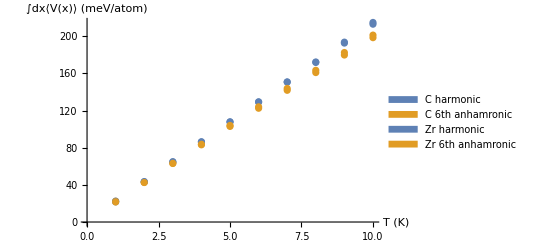

```mathematica
The potential V(x) expectation integrated over position;
(*carbon and zirconium harmonic and 6th order anharmonic Potential V[X] el-ph energy*)cpdata={Table[densMatExpect[Evaluate@V[1,2,x][[1]],charval,charvec,500*i],{i,1,10}],Table[densMatExpect[Evaluate@V[1,6,x][[1]],canhval,canhvec,500*i],{i,1,10}]};
zpdata={Table[densMatExpect[Evaluate@V[2,2,x][[1]],zharval,zharvec,500*i],{i,1,10}],Table[densMatExpect[Evaluate@V[2,6,x][[1]],zanhval,zanhvec,500*i],{i,1,10}]};
"Carbon harmonic and 6th order anharmonic:"
cpdata//TableForm
"Zr harmonic and 6th order anharmonic:"
zpdata//TableForm
plotOpts2={AxesLabel->{"T (K)","∫dx⟨V(x)⟩ (meV/atom)"}};
Show[ListPlot[cpdata,Evaluate@plotOpts2,PlotLegends->SwatchLegend[{"C harmonic","C 6th anhamronic"}]],ListPlot[zpdata,PlotLegends->SwatchLegend[{"Zr harmonic","Zr 6th anhamronic"}]]]
```

```mathematica
Position representation reduced density matrix expectation of the identity;
The identity expectation is plotted as a function of positions along (001) for Zr and C at 500K intervals from up to 5000K
```

2500000 a along and as at C expectation for from function identity intervals is K^2 of plotted positions The to up Zr

Carbon occupation vs distance:

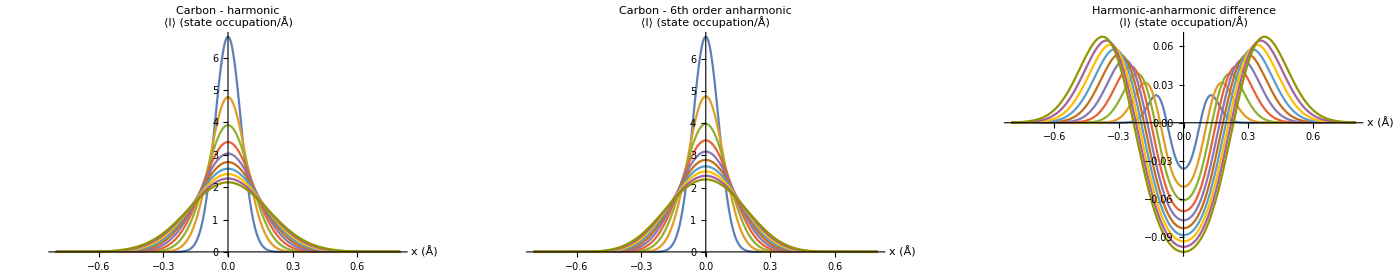

Zr occupation vs distance:

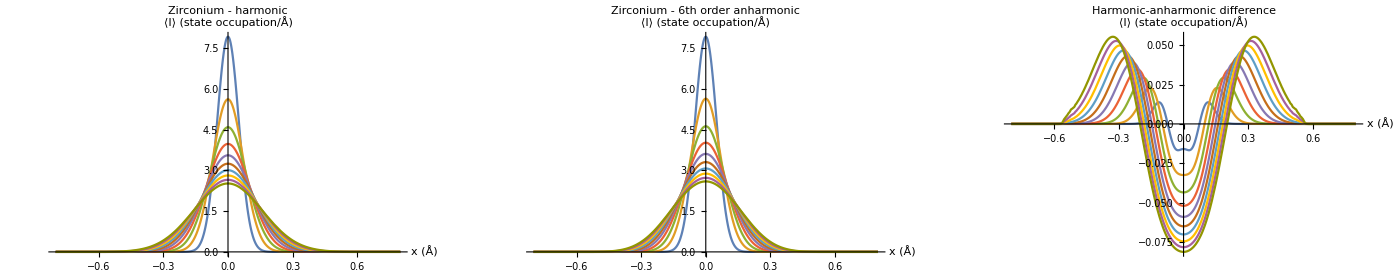

```mathematica
(*Options*)
B=0.8;
plotOpts2={AxesLabel->{"x (Å)","⟨I⟩ (state occupation/Å)"}};
(*carbon and zr harmonic and 6th order anharmonic I expectation and difference*)
"Carbon occupation vs distance:"
GraphicsGrid[
{{Plot[Evaluate@Table[densMatOperator[1,charval,charvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Carbon - harmonic",Evaluate@plotOpts2],Plot[Evaluate@Table[densMatOperator[1,canhval,canhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Carbon - 6th order anharmonic",Evaluate@plotOpts2],Plot[Evaluate@Table[densMatOperator[1,charval,charvec,500*i]-densMatOperator[1,canhval,canhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Harmonic-anharmonic difference",Evaluate@plotOpts2]}},ImageSize->1400]
"Zr occupation vs distance:"
GraphicsGrid[
{{Plot[Evaluate@Table[densMatOperator[1,zharval,zharvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Zirconium - harmonic",Evaluate@plotOpts2],Plot[Evaluate@Table[densMatOperator[1,zanhval,zanhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Zirconium - 6th order anharmonic",Evaluate@plotOpts2],Plot[Evaluate@Table[densMatOperator[1,zharval,zharvec,500*i]-densMatOperator[1,zanhval,zanhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Harmonic-anharmonic difference",Evaluate@plotOpts2]}},ImageSize->1400]
```

Carbon harmonic and 6th order anharmonic:

1. | 1. | 1. | 1. | 1. | 0.999999 | 0.999994 | 0.999975 | 0.99993 | 0.999839
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999

Zr harmonic and 6th order anharmonic:

1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999 | 1. | 0.999998
1. | 1. | 1. | 1. | 1. | 0.999999 | 1. | 0.999999 | 1. | 1.

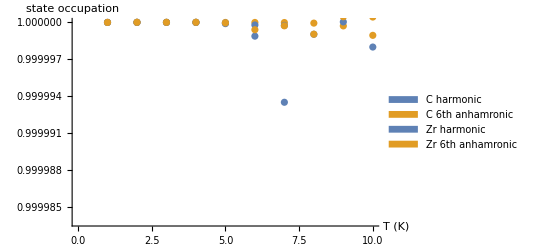

```mathematica
The identity expectation integrated over position;
(*carbon and zirconium harmonic and 6th order anharmonic identity*)cpdata2={Table[densMatExpect[1,charval,charvec,500*i],{i,1,10}],Table[densMatExpect[1,canhval,canhvec,500*i],{i,1,10}]};
zpdata2={Table[densMatExpect[1,zharval,zharvec,500*i],{i,1,10}],Table[densMatExpect[1,zanhval,zanhvec,500*i],{i,1,10}]};
"Carbon harmonic and 6th order anharmonic:"
cpdata2//TableForm
"Zr harmonic and 6th order anharmonic:"
zpdata2//TableForm
plotOpts2={AxesLabel->{"T (K)","state occupation"}};
Show[ListPlot[cpdata2,Evaluate@plotOpts2,PlotLegends->SwatchLegend[{"C harmonic","C 6th anhamronic"}]],ListPlot[zpdata2,PlotLegends->SwatchLegend[{"Zr harmonic","Zr 6th anhamronic"}]]]
```

```mathematica
Position representation reduced density matrix expectation of the identity;
The position operator expectation is plotted as a function of positions along (001) for Zr and C at 500K intervals from up to 5000K
```

Carbon occupation vs distance: §

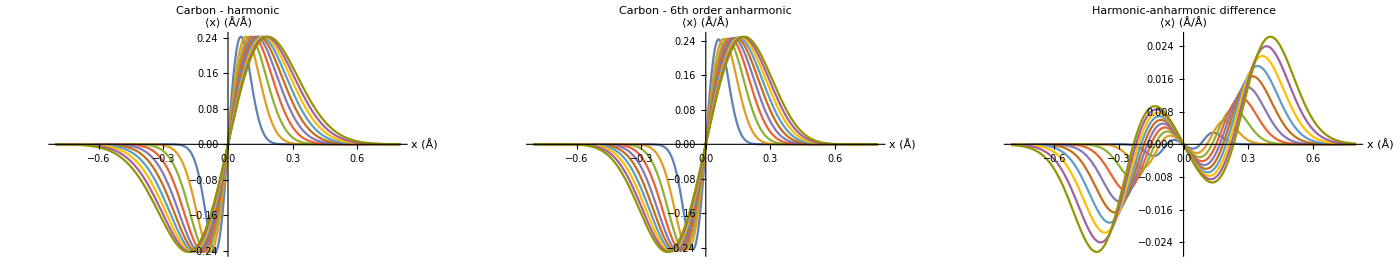

Zr occupation vs distance:

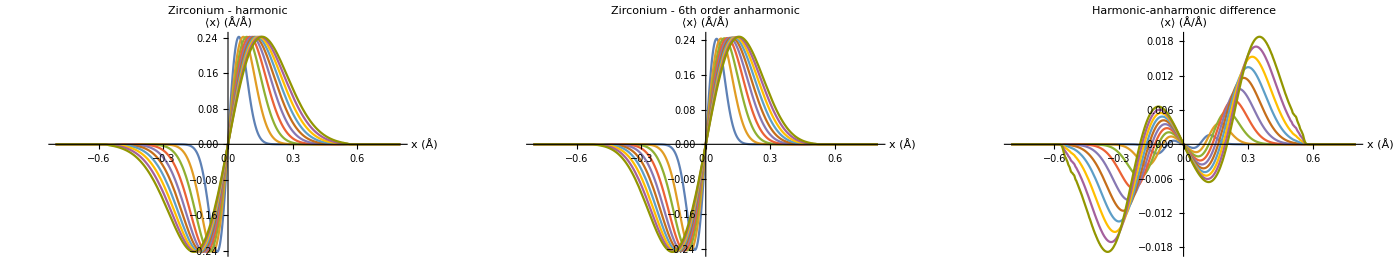

```mathematica
(*Options*)
B=0.8;
plotOpts3={AxesLabel->{"x (Å)","⟨x⟩ (Å/Å)"}};
(*carbon and zr harmonic and 6th order anharmonic I expectation and difference*)
"Carbon occupation vs distance:"§
GraphicsGrid[
{{Plot[Evaluate@Table[densMatOperator[x,charval,charvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Carbon - harmonic",Evaluate@plotOpts3],Plot[Evaluate@Table[densMatOperator[x,canhval,canhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Carbon - 6th order anharmonic",Evaluate@plotOpts3],Plot[Evaluate@Table[densMatOperator[x,charval,charvec,500*i]-densMatOperator[x,canhval,canhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Harmonic-anharmonic difference",Evaluate@plotOpts3]}},ImageSize->1400]
"Zr occupation vs distance:"
GraphicsGrid[
{{Plot[Evaluate@Table[densMatOperator[x,zharval,zharvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Zirconium - harmonic",Evaluate@plotOpts3],Plot[Evaluate@Table[densMatOperator[x,zanhval,zanhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Zirconium - 6th order anharmonic",Evaluate@plotOpts3],Plot[Evaluate@Table[densMatOperator[x,zharval,zharvec,500*i]-densMatOperator[x,zanhval,zanhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Harmonic-anharmonic difference",Evaluate@plotOpts3]}},ImageSize->1400]
```

```mathematica
RMS Position representation reduced density matrix expectation of the identity;
The position operator expectation is plotted as a function of positions along (001) for Zr and C at 500K intervals from up to 5000K
```

Carbon occupation vs distance: §

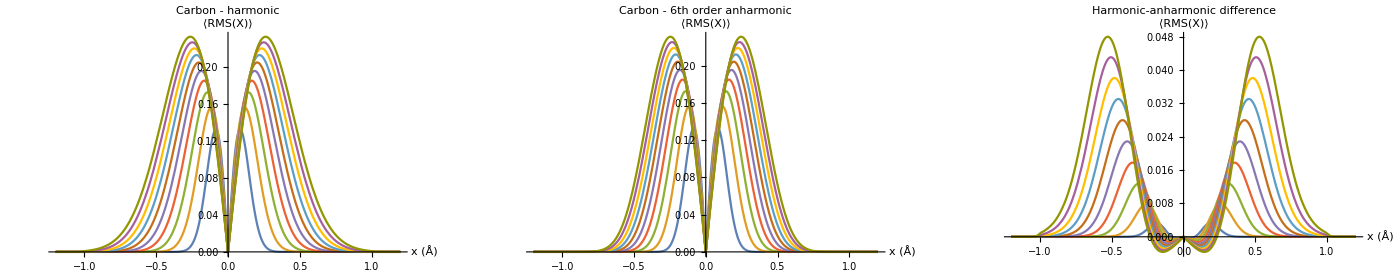

Zr occupation vs distance:

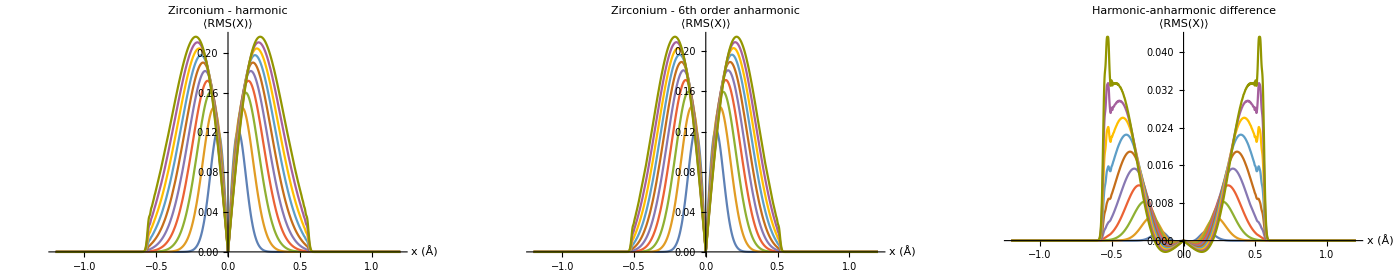

```mathematica
(*Options*)
B=1.2;
plotOpts3={AxesLabel->{"x (Å)","⟨RMS(X)⟩"}};
(*carbon and zr harmonic and 6th order anharmonic I expectation and difference*)
"Carbon occupation vs distance:"§
GraphicsGrid[
{{Plot[Evaluate@Table[Sqrt@densMatOperator[x^2,charval,charvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Carbon - harmonic",Evaluate@plotOpts3],Plot[Evaluate@Table[Sqrt@densMatOperator[x^2,canhval,canhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Carbon - 6th order anharmonic",Evaluate@plotOpts3],Plot[Evaluate@Table[Sqrt@densMatOperator[x^2,charval,charvec,500*i]-Sqrt@densMatOperator[x^2,canhval,canhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Harmonic-anharmonic difference",Evaluate@plotOpts3]}},ImageSize->1400]
"Zr occupation vs distance:"
GraphicsGrid[
{{Plot[Evaluate@Table[Sqrt@densMatOperator[x^2,zharval,zharvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Zirconium - harmonic",Evaluate@plotOpts3],Plot[Evaluate@Table[Sqrt@densMatOperator[x^2,zanhval,zanhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Zirconium - 6th order anharmonic",Evaluate@plotOpts3],Plot[Evaluate@Table[Sqrt@densMatOperator[x^2,zharval,zharvec,500*i]-Sqrt@densMatOperator[x^2,zanhval,zanhvec,500*i],{i,1,10}],{x,-B,B},PlotRange->All,PlotLabel->"Harmonic-anharmonic difference",Evaluate@plotOpts3]}},ImageSize->1400]
```